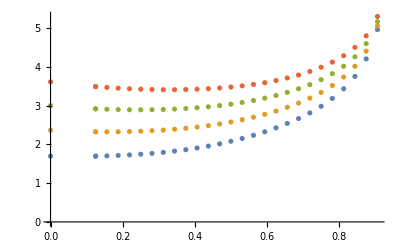

```mathematica
a={{0,1.693147},{0.125000,1.694818},{0.125000,1.694818},{0.156250,1.702468},{0.187500,1.713139},{0.218750,1.727117},{0.250000,1.744764},{0.281250,1.766497},{0.312500,1.792789},{0.343750,1.824162},{0.375000,1.861197},{0.406250,1.904493},{0.437500,1.954648},{0.468750,2.012238},{0.500000,2.077714},{0.531250,2.151283},{0.562500,2.233051},{0.593750,2.323575},{0.625000,2.424229},{0.656250,2.537012},{0.687500,2.664582},{0.718750,2.810637},{0.750000,2.980576},{0.781250,3.182745},{0.812500,3.431066},{0.843750,3.751567},{0.875000,4.202609},{0.906250,4.957573}};
a2={{0,2.362954},{0.125000,2.323257},{0.125000,2.323257},{0.156250,2.322063},{0.187500,2.324053},{0.218750,2.329328},{0.250000,2.338087},{0.281250,2.350598},{0.312500,2.367185},{0.343750,2.388220},{0.375000,2.414117},{0.406250,2.445322},{0.437500,2.482314},{0.468750,2.525596},{0.500000,2.575708},{0.531250,2.633241},{0.562500,2.698887},{0.593750,2.773506},{0.625000,2.858230},{0.656250,2.954594},{0.687500,3.064735},{0.718750,3.191703},{0.750000,3.340007},{0.781250,3.516665},{0.812500,3.733418},{0.843750,4.012222},{0.875000,4.402299},{0.906250,5.051905}};
a3={{0,2.997490},{0.125000,2.915240},{0.125000,2.915240},{0.156250,2.903981},{0.187500,2.896094},{0.218750,2.891546},{0.250000,2.890411},{0.281250,2.892847},{0.312500,2.899077},{0.343750,2.909380},{0.375000,2.924087},{0.406250,2.943579},{0.437500,2.968284},{0.468750,2.998685},{0.500000,3.035327},{0.531250,3.078832},{0.562500,3.129929},{0.593750,3.189499},{0.625000,3.258639},{0.656250,3.338772},{0.687500,3.431814},{0.718750,3.540440},{0.750000,3.668568},{0.781250,3.822259},{0.812500,4.011620},{0.843750,4.255510},{0.875000,4.596146},{0.906250,5.162084}};
a4={{0,3.611379},{0.125000,3.488045},{0.125000,3.488045},{0.156250,3.466246},{0.187500,3.448007},{0.218750,3.433198},{0.250000,3.421806},{0.281250,3.413908},{0.312500,3.409651},{0.343750,3.409247},{0.375000,3.412966},{0.406250,3.421133},{0.437500,3.434134},{0.468750,3.452412},{0.500000,3.476484},{0.531250,3.506949},{0.562500,3.544515},{0.593750,3.590032},{0.625000,3.644551},{0.656250,3.709409},{0.687500,3.786369},{0.718750,3.877861},{0.750000,3.987387},{0.781250,4.120312},{0.812500,4.285518},{0.843750,4.499486},{0.875000,4.798979},{0.906250,5.296732}};
ListPlot[{a,a2,a3,a4}]
```

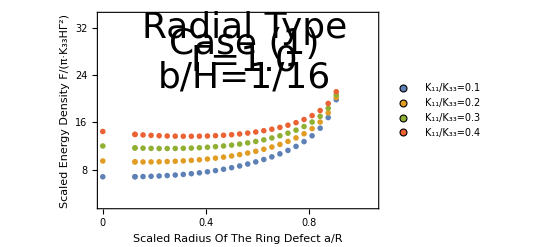

```mathematica
aa=a*Table[{1,4},{i,0,27}];
aa2=a2*Table[{1,4},{i,0,27}];
aa3=a3*Table[{1,4},{i,0,27}];
aa4=a4*Table[{1,4},{i,0,27}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{8,16,24,32,40},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{2,34}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{0.55,32}],Text[Style["Case (1)",Directive[Black,36]],{0.55,29.2}],Text[Style["Γ=1.0",Directive[Black,36]],{0.55,26.4}],Text[Style["b/H=1/16",Directive[Black,36]],{0.55,23.6}]}]
```